```mathematica
Examples of Electric fields E and corresponding vector potentials A:
```

```mathematica
Definition of the electric field profiles:
```

```mathematica
A=.;t0=.;t1=.;ω=.;τ=.;
Ef[t_]:=A*Cos[ω*(t-t0)]*Exp[-((t-t0)^2)/(2*τ^2)]
Econstant[t_]:=A*HeavisideTheta[t-t0]*HeavisideTheta[t1-t]
Ramp[t_]:=(1/2-3/4*Cos[π*t/t0]+1/4*Cos[π*t/t0]^3)
Esmooth[t_]:=A*Ramp[t]*HeavisideTheta[t0-t]+Econstant[t]
```

```mathematica
Get the corresponding vector potential by indefinite integration :
```

```mathematica
FullSimplify[Integrate[Ef[t],t]]
FullSimplify[Integrate[Econstant[t],t]]
FullSimplify[Integrate[Esmooth[t],t]]
```

(8.68762×10^-49+9.3647×10^-63 ⅈ) Erf[(-4.44288+10.6066 ⅈ)+1.41421 t]-(9.3647×10^-63+8.68762×10^-49 ⅈ) Erfi[(10.6066-4.44288 ⅈ)+(0.+1.41421 ⅈ) t]

-20 (-4+t) HeavisideTheta[-4+t]+20 (-π+t) HeavisideTheta[-π+t]

5/12 (24 t-48 (-4+t) HeavisideTheta[-4+t]-27 Sin[t]+HeavisideTheta[-π+t] (-24 π+24 t+27 Sin[t]-Sin[3 t])+Sin[3 t])

```mathematica
Copy/Paste Vector potential to new functions:
```

```mathematica
Af[t_]:=1/2 A ⅇ^(-1/2 τ^2 ω^2) √(π/2) τ (Erf[(t-t0-ⅈ τ^2 ω)/(√2 τ)]+Erf[(t-t0+ⅈ τ^2 ω)/(√2 τ)])
Aconstant[t_]:=A HeavisideTheta[t-t0] (t-t0+(-t+t1) HeavisideTheta[t-t1]+(t0-t1) HeavisideTheta[t0-t1])
Asmooth[t_]:=1/(48 π)A (24 π (t+(t-t0) HeavisideTheta[t-t0]+2 (-t+t1) HeavisideTheta[t-t0,t-t1]+2 (t0-t1) HeavisideTheta[t-t0,t0-t1])+27 t0 (-1+HeavisideTheta[t-t0]) Sin[(π t)/t0]-t0 (-1+HeavisideTheta[t-t0]) Sin[(3 π t)/t0])
```

```mathematica
Set specific value of the parametrs appearing in equations above :
```

```mathematica
A=20 
 t0=π
 t1=4  
ω=30 
 τ=1.0/(2π)
```

20

π

4

30

0.159155

```mathematica
Plot  of impulse - like profile :
```

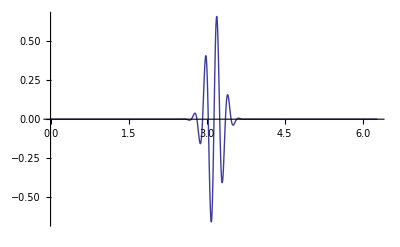

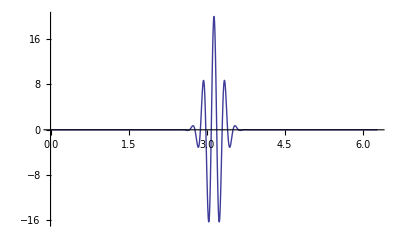

```mathematica
Plot[Re[Af[x]],{x,0,2π},PlotRange->Full]
Plot[Ef[x],{x,0,2π},PlotRange->Full]
```

```mathematica
Plot of the constant profile :
```

```mathematica
Plot[Econstant[x],{x,0,5},PlotRange->Full]
Plot[Re[Aconstant[x]],{x,0,5},PlotRange->Full]
```

```mathematica
Plot of the ramp profile :
```

```mathematica
Plot[Esmooth[x],{x,0,5},PlotRange->Full]
Plot[Re[Asmooth[x]],{x,0,5},PlotRange->Full]
```